# Model of N-dependent competition between thermal tolerant and intolerant strains

Developed for Aranguren-Gassis et al. 2019 by CT Kremer and CA Klausmeier.

### Initial reflections on parameter values and constraints:

```mathematica
(* r1 limiting *)
(b1*v1/(q0+q1 p))* E^(b2 T)- (d1/p)* E^(d2 T)

(* r2 limiting *)
(b1*v2/q2) E^(b2 T) -( d1/p)* E^(d2 T)
```

-(d1 ⅇ^(d2 T))/p+(b1 ⅇ^(b2 T) v1)/(q0+p q1)

-(d1 ⅇ^(d2 T))/p+(b1 ⅇ^(b2 T) v2)/q2

These are the curves I can actually fit to the experimental data. If we exclude data from T = 10 C, the model fits suggest that at high resources, limitation is driven by r2.

I find that: d1 = 4.8 e -6 and p = 1.919
However, I don’t have direct estimates of b1 from the second model - rather, the values I’ve estimated imply that:
	 0.226 = (b1*v2/q2)
And I have no estimates or constraints at all for:
	q0, q1, v1, k1, k2
Except that whatever their values, R2 should be limiting at “high” resource supply.

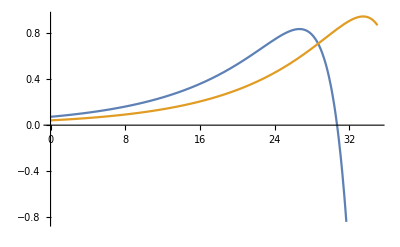

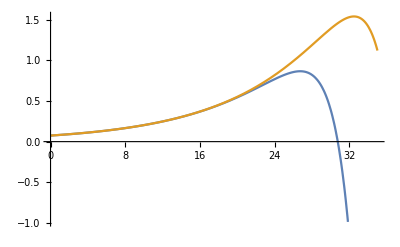

```mathematica
b1=0.224/3;
d1=3.059*10^-7/3;
b2=0.1;
d2=0.5;
q0=1;q1=0.1;
Clear[p];

(* limited by r1 *)
func[T_,p_]:=(b1 E^(b2 T)/( q0+q1*p)-(d1/p)* E^(d2 T));
Plot[{func[T,0.3],func[T,8]},{T,0,35}]

(* limited by r2 *)
func2[T_,p_]:=(b1 E^(b2 T)-(d1/p)* E^(d2 T));
Plot[{func2[T,0.3],func2[T,3]},{T,0,35}]
```

### Obtain & load EcoEvo package

Note: this Mathematica package was developed by CA Klausmeier. Newer versions are now available, with streamlined syntax and other improvements. However, the code below was developed using an older version of the package (0.9.3)

```mathematica
(* FIRST TIME ONLY: to install the relevant version of this package, you need to run the following line  *)
(*PacletInstall["https://github.com/cklausme/EcoEvo/releases/download/v0.9.3/EcoEvo-0.9.3.paclet"]*)
```

```mathematica
(* To load the package: *)
<<EcoEvo`
```

EcoEvo Package Version 0.9.3β (September 16, 2018)

### Set up model

Define core equations

```mathematica
b[p_,r1_,r2_,T_]:=b1 E^(b2 T)Min[v1/(q0+q1 p)r1/(r1+k1),v2/q2 r2/(r2+k2)];
d[p_,T_]:=d1 E^(d2 T)/p;

dn[i_]:=(b[Subscript[p, i],r1[t],r2[t],T]-d[Subscript[p, i],T])*Subscript[n, i][t];

dr1:=-Sum[b[Subscript[p, i],r1[t],r2[t],T]*(q0+q1 Subscript[p, i])*Subscript[n, i][t],{i,Nsp[1]}];
dr2:=-Sum[b[Subscript[p, i],r1[t],r2[t],T]*(q2)*Subscript[n, i][t],{i,Nsp[1]}];
```

Define model for EcoEvo package

```mathematica
SetModel[{ModelType->"ContinuousTime",Period->τ,
Aux[1]->{Variable->r1,Equation:>dr1},
Aux[2]->{Variable->r2,Equation:>dr2},
Guild[1]->{
Component[1]->{Variable->n,Equation-> dn},
Trait[1]->{Variable->p,Range->Interval[{0,∞}]}
},
WhenEvents->{WhenEvent[Mod[t,τ],{ntot=Sum[Subscript[n, i][t],{i,Nsp[1]}],r1[t]->rin1,r2[t]->rin2,Subscript[n, 1][t]->n0*Subscript[n, 1][t]/ntot,Subscript[n, 2][t]->n0*Subscript[n, 2][t]/ntot}]}
}];
```

### Set up model parameters

See details in Supporting information: Appendix 1 and R script TPC_fitting_for_mma_model_unweighted_final_041818.R

```mathematica
(* estimated parameters *)
α=0.31673;
δ1=1.9926*10^-8;
δ2=7.6312*10^-9;
b2=0.04854806212876125;
d2=0.5426802449468293;

(* assumptions *)
b1=5*10^-1;
p1g=1; (* unprotected strain *)
v1=15; 
q0=0.5; 
q1=5.25; (* controls cost of protection! *)
q2=2; 
k1=6;k2=10; 
n0=rin1/10;
τ=3;

(* implications *)
d1=δ1;
p2g=δ1/δ2;(* protected strain *)
v2=α*q2/b1;
```

```mathematica
(* checks *)
α*q2/b1
{v2/q2,v1/(q0+q1*p1g),v1/(q0+q1*p2g)}
v2/q2 ≤v1/(q0+q1*p1g)
v2/q2 ≤v1/(q0+q1*p2g)
884./(884+k1)
```

1.26692

{0.63346,2.6087,1.05571}

True

True

0.993258

Import empirical data used to parameterize thermal performance curves of tolerant and intolerant strains:

```mathematica
dat=Import["/Users/colin/Dropbox/EvolutionPaper_SharedFolder/Data/data_for_tpc_fits_to_parameterize_model.csv"];
```

```mathematica
dat=Transpose[dat];
```

```mathematica
rvec=dat[[2,2;;]];
tvec=dat[[4,2;;]];
casevec=dat[[6,2;;]];
```

```mathematica
rvecLOW=dat[[2,2;;43]];
tvecLOW=dat[[4,2;;43]];
casevecLOW=dat[[6,2;;43]];
rvecHIGH=dat[[2,44;;]];
tvecHIGH=dat[[4,44;;]];
casevecHIGH=dat[[6,44;;]];
```

Here’s what it looks like:

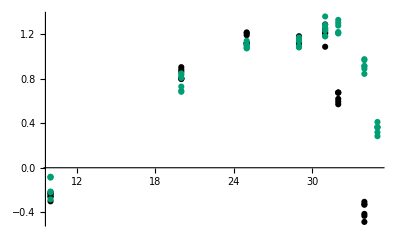

```mathematica
ListPlot[{Transpose[{tvecLOW,rvecLOW}],Transpose[{tvecHIGH,rvecHIGH}]},PlotStyle->{Black,RGBColor["#009E73"]}]
```

### Explore model

Consider effects of N supply on thermal performance curves (TPCs)

```mathematica
Clear[r1,r2]
```

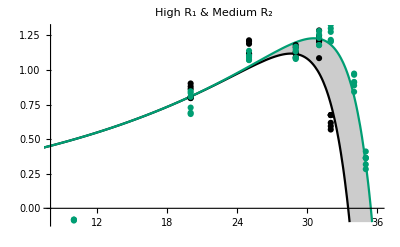

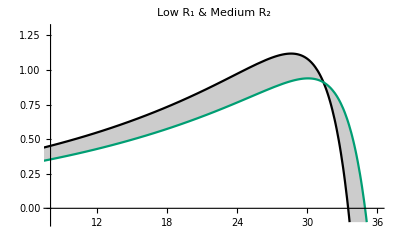

```mathematica
r1tmpA=884;r1tmpB=5;r2tmp=300;

Show[Plot[{b[p1g,r1tmpA,r2tmp,T]-d[p1g,T],b[p2g,r1tmpA,r2tmp,T]-d[p2g,T]},{T,0,36},PlotRange->{{8,36},{-0.1,1.3}},Filling->{1->{2}},PlotLabel->"High R_1 & Medium R_2",PlotStyle->{Black,RGBColor["#009E73"]}],ListPlot[{Transpose[{tvecLOW,rvecLOW}],Transpose[{tvecHIGH,rvecHIGH}]},PlotStyle->{Black,RGBColor["#009E73"]}]]

Plot[{b[p1g,r1tmpB,r2tmp,T]-d[p1g,T],b[p2g,r1tmpB,r2tmp,T]-d[p2g,T]},{T,0,36},PlotRange->{{8,36},{-0.1,1.3}},Filling->{1->{2}},PlotLabel->"Low R_1 & Medium R_2",PlotStyle->{Black,RGBColor["#009E73"]}]
```

Run competition model under N-limiting and N-replete conditions

```mathematica
Clear[r1,r2];
tmax=67τ;

T=31;
rin2=300;

(* N-limiting results *)
rin1=5;
n0=rin1/100;
sollo=EcoSim[{Subscript[p, 1]->p1g,Subscript[p, 2]->p2g},{r1->0,r2->0,Subscript[n, 1]->n0,Subscript[n, 2]->n0*10^-8},tmax];

(* N-replete results *)
rin1=884;
solhi=EcoSim[{Subscript[p, 1]->p1g,Subscript[p, 2]->p2g},{r1->0,r2->0,Subscript[n, 1]->n0,Subscript[n, 2]->n0*10^-8},tmax];
```

Generate plot of TPCs and temporal dynamics under limiting and replete nutrients

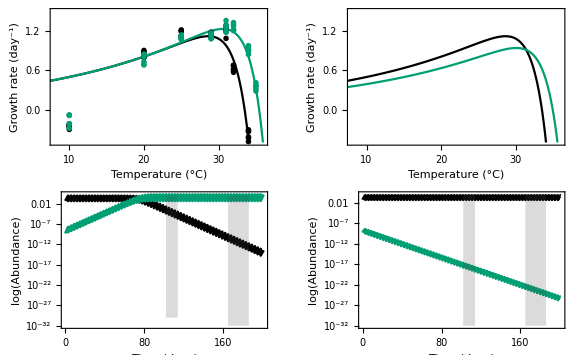

```mathematica
panelA=Show[Plot[{b[p1g,r1tmpA,r2tmp,T]-d[p1g,T],b[p2g,r1tmpA,r2tmp,T]-d[p2g,T]},{T,0,36},PlotRange->{{8,36},{-0.5,1.5}},PlotLabel->" ",PlotStyle->{Directive[Black],Directive[ RGBColor["#009E73"]]},Frame->{{True,False},{True,False}},FrameLabel->{"Temperature (°C)","Growth rate  (day^-1)"},LabelStyle->{FontFamily->"Times New Roman",Black}],ListPlot[{Transpose[{tvecLOW,rvecLOW}],Transpose[{tvecHIGH,rvecHIGH}]},PlotMarkers->{-Graphics-,-Graphics-},PlotStyle->{Directive[PointSize->Small,Black],Directive[RGBColor["#009E73"],PointSize->Small]}]];
panelB=Plot[{b[p1g,r1tmpB,r2tmp,T]-d[p1g,T],b[p2g,r1tmpB,r2tmp,T]-d[p2g,T]},{T,0,36},PlotRange->{{8,36},{-0.5,1.5}},PlotLabel->" ",PlotStyle->{Directive[Black],Directive[ RGBColor["#009E73"]]},Frame->{{True,False},{True,False}},FrameLabel->{"Temperature (°C) \n","Growth rate  (day^-1)"},LabelStyle->{FontFamily->"Times New Roman",Black}];
panelC=Show[PlotDynamics[solhi,{n},PlotPoints->200,Logged->True,PlotLabel->" ",PlotStyle->{Directive[Black,Thickness[0.005]], Directive[RGBColor["#009E73"],Thickness[0.005]]},Frame->{{True,False},{True,False}},FrameLabel->{"Time (days)","log(Abundance)"}],ListLogPlot[{{102,10^-30},{114,10^-30}},Joined->True,Filling->Top,FillingStyle->GrayLevel[0.3,0.2],PlotStyle->{GrayLevel[0.3,0]}],ListLogPlot[{{165,10^-32},{186,10^-32}},Joined->True,Filling->Top,FillingStyle->GrayLevel[0.3,0.2],PlotStyle->{GrayLevel[0.3,0]}],LabelStyle->{FontFamily->"Times New Roman",Black}];
panelD=Show[PlotDynamics[sollo,{n},PlotPoints->200,Logged->True,PlotLabel->" ",PlotStyle->{Directive[Black,Thickness[0.005]], Directive[RGBColor["#009E73"],Thickness[0.005]]},Frame->{{True,False},{True,False}},FrameLabel->{"Time (days)","log(Abundance)"}],ListLogPlot[{{102,10^-32},{114,10^-32}},Joined->True,Filling->Top,FillingStyle->GrayLevel[0.3,0.2],PlotStyle->{GrayLevel[0.3,0]}],ListLogPlot[{{165,10^-32},{186,10^-32}},Joined->True,Filling->Top,FillingStyle->GrayLevel[0.3,0.2],PlotStyle->{GrayLevel[0.3,0]}],LabelStyle->{FontFamily->"Times New Roman",Black}];

Fig4=GraphicsGrid[{{panelA,panelB},{panelC,panelD}},ImageSize->Large]
```

```mathematica
Export["Fig4.pdf",leg]
```

Legend for use in post-processing of graphic:

```mathematica
leg=LineLegend[{Directive[Thick,Black],Directive[Thick,RGBColor["#009E73"]]},{"Intolerant strain","Tolerant strain"},LabelStyle->{FontFamily->"Times New Roman"}]
```

```mathematica
Export["Fig4_legend.pdf",leg]
```

### Comparing carrying capacity (evidence for 2 resource system)

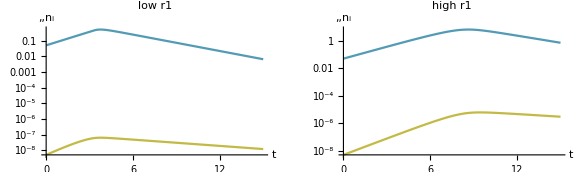

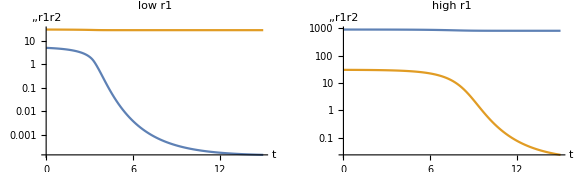

```mathematica
Clear[r1,r2];
τ=15;
tmax=1τ;

T=31;
rin2=30;

rin1=5;
n0=rin1/100;
sollo=EcoSim[{Subscript[p, 1]->p1g,Subscript[p, 2]->p2g},{r1->0,r2->0,Subscript[n, 1]->n0,Subscript[n, 2]->n0*10^-7},tmax];

rin1=884;
(*n0=rin2/100;*)
solhi=EcoSim[{Subscript[p, 1]->p1g,Subscript[p, 2]->p2g},{r1->0,r2->0,Subscript[n, 1]->n0,Subscript[n, 2]->n0*10^-7},tmax];

GraphicsRow[{
PlotDynamics[sollo,{n},PlotPoints->100,Logged->True,PlotLabel->"low r1"],PlotDynamics[solhi,{n},PlotPoints->100,Logged->True,PlotLabel->"high r1"]
},ImageSize->Large,PlotLabel->"T=31"]
GraphicsRow[{
PlotDynamics[sollo,{r1,r2},PlotPoints->100,Logged->True,PlotLabel->"low r1"],PlotDynamics[solhi,{r1,r2},PlotPoints->100,Logged->True,PlotLabel->"high r1"]
},ImageSize->Large,PlotLabel->"T=31"]
```

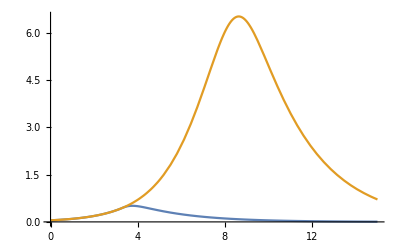

```mathematica
Plot[{(Subscript[n, 1][t]+Subscript[n, 2][t])/.sollo,(Subscript[n, 1][t]+Subscript[n, 2][t])/.solhi},{t,0,tmax}]
```

```mathematica
NMaximize[(Subscript[n, 1][t]+Subscript[n, 2][t])/.sollo,{t,4,8}]
NMaximize[(Subscript[n, 1][t]+Subscript[n, 2][t])/.solhi,{t,8,12}]
```

{0.511304,{t→3.75523}}

{6.52744,{t→8.63567}}

```mathematica
6.527439000401393/0.5113036905023219
```

12.7663

This is a pretty reasonable comparison of peak densities, relative to what we see in the experiment. Note that these curves appear unimodal b/c we’re just tracking the abundance of ‘live’ cells here, and the dead ones necessarily accumulate after R* is reached. Fluorescence or absorbance based measures would not distinguish between the two.